# Motor Primitives

## Init

### settings

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tonegas/University/Teaching/corso-intelligent-vehicles-and-autonomous-driving

```mathematica
packageDir=FileNameJoin[{NotebookDirectory[],"generated_code"}]
```

/Users/tonegas/University/Teaching/corso-intelligent-vehicles-and-autonomous-driving/generated_code

## General solution of longitudinal optimal control problem using Hamiltonian

### Matrix definition of the plant

s[t] : longitudinal position
v[t] : longitudinal velocity
a[t] : longitudinal acceleration
j[t] : longitudinal jerk

Matrix form of the plant

```mathematica
Asys={{0,1,0},{0,0,1},{0,0,0}};
Bsys={{0},{0},{1}};
```

State variables

```mathematica
xv={s[t],v[t],a[t]};
uv={j[t]};
```

Plant definition

```mathematica
plant=Asys.xv+Bsys.uv;TraditionalForm@TableForm@plant
```

v(t)
a(t)
j(t)

### Lagrange formulation

Function to be minimized,  minimum jerk

```mathematica
criterion=j[t]^2;TraditionalForm@criterion (* minimum jerk *)
```

(j(t))^2

Definition of Lagrange multipliers

```mathematica
lambda={λ1[t],λ2[t],λ3[t]};
```

Hamiltonian function definition

```mathematica
H=criterion + plant . lambda; TraditionalForm@TableForm@H
```

a(t) λ2(t)+j(t) λ3(t)+(j(t))^2+λ1(t) v(t)

Variables

```mathematica
vars=xv∪lambda;vars
```

{a[t],s[t],v[t],λ1[t],λ2[t],λ3[t]}

### Optimal control solution

```mathematica
optimalinput=Flatten@Solve[D[H, j[t]]==0,j[t]]
```

{j[t]→-λ3[t]/2}

First condition x'[t] = ∂H/∂λ

```mathematica
cond1=Table[D[xv,t][[i]]==Table[D[H,l],{l,lambda}][[i]],{i,1,3}]
```

{s'[t]==v[t],v'[t]==a[t],a'[t]==j[t]}

Second condition λ'[t] = -∂H/∂x

```mathematica
cond2=Table[D[lambda,t][[i]]==-Table[D[H,x],{x,xv}][[i]],{i,1,3}]
```

{λ1'[t]==0,λ2'[t]==-λ1[t],λ3'[t]==-λ2[t]}

#### Boundary conditions.

```mathematica
ic={s[0]==0,v[0]==v0,a[0]==a0};TraditionalForm@ic
```

{s(0)==0,v(0)==v0,a(0)==a0}

```mathematica
fc={s[T]==sf,v[T]==vf,a[T]==af};TraditionalForm@fc
```

{s(T)==sf,v(T)==vf,a(T)==af}

#### Optimal control BVP

```mathematica
optimalinput
```

{j[t]→-λ3[t]/2}

```mathematica
cond1/.optimalinput
```

{s'[t]==v[t],v'[t]==a[t],a'[t]==-λ3[t]/2}

```mathematica
odebvp=(cond1/.optimalinput)∪cond2∪ ic ∪fc;TraditionalForm@TableForm@odebvp
```

a(0)==a0
a(T)==af
s(0)==0
s(T)==sf
v(0)==v0
v(T)==vf
a'(t)==-(λ3(t))/2
s'(t)==v(t)
v'(t)==a(t)
λ1'(t)==0
λ2'(t)==-λ1(t)
λ3'(t)==-λ2(t)

#### Solution of the Optimal Control Problem

```mathematica
sol=Map[FullSimplify,Flatten@DSolve[odebvp,vars,t]];
```

```mathematica
sol
```

{a[t]→(60 sf t (2 t^2-3 t T+T^2)+T (-a0 (t-T) T (10 t^2-8 t T+T^2)+af t T (10 t^2-12 t T+3 T^2)-12 t (t-T) (5 t (v0+vf)-T (3 v0+2 vf))))/T^5,s[t]→(2 sf t^3 (6 t^2-15 t T+10 T^2)+t T (-t+T) ((-t+T) (t T (af t+a0 (-t+T))+2 (-t+T) (3 t+T) v0)+2 t^2 (3 t-4 T) vf))/(2 T^5),v[t]→(60 sf t^2 (t-T)^2+T (-t+T) (t T (a0 (5 t-2 T) (t-T)+af t (-5 t+3 T))+2 (-3 t+T) (-t+T) (5 t+T) v0)-2 t^2 (5 t-6 T) (3 t-2 T) T vf)/(2 T^5),λ1[t]→(120 (-12 sf+T (a0 T-af T+6 (v0+vf))))/T^5,λ2[t]→-(24 (30 sf (-2 t+T)+T (a0 (5 t-3 T) T+af T (-5 t+2 T)+30 t (v0+vf)-2 T (8 v0+7 vf))))/T^5,λ3[t]→(6 (-20 sf (6 t^2-6 t T+T^2)+T (-af T (10 t^2-8 t T+T^2)+a0 T (10 t^2-12 t T+3 T^2)+60 t^2 v0-64 t T v0+12 T^2 v0+60 t^2 vf-56 t T vf+8 T^2 vf)))/T^5}

```mathematica
solLongOCP =  Flatten@{sol,j[t]->(j[t]/.optimalinput/.sol)}
```

{a[t]→(60 sf t (2 t^2-3 t T+T^2)+T (-a0 (t-T) T (10 t^2-8 t T+T^2)+af t T (10 t^2-12 t T+3 T^2)-12 t (t-T) (5 t (v0+vf)-T (3 v0+2 vf))))/T^5,s[t]→(2 sf t^3 (6 t^2-15 t T+10 T^2)+t T (-t+T) ((-t+T) (t T (af t+a0 (-t+T))+2 (-t+T) (3 t+T) v0)+2 t^2 (3 t-4 T) vf))/(2 T^5),v[t]→(60 sf t^2 (t-T)^2+T (-t+T) (t T (a0 (5 t-2 T) (t-T)+af t (-5 t+3 T))+2 (-3 t+T) (-t+T) (5 t+T) v0)-2 t^2 (5 t-6 T) (3 t-2 T) T vf)/(2 T^5),λ1[t]→(120 (-12 sf+T (a0 T-af T+6 (v0+vf))))/T^5,λ2[t]→-(24 (30 sf (-2 t+T)+T (a0 (5 t-3 T) T+af T (-5 t+2 T)+30 t (v0+vf)-2 T (8 v0+7 vf))))/T^5,λ3[t]→(6 (-20 sf (6 t^2-6 t T+T^2)+T (-af T (10 t^2-8 t T+T^2)+a0 T (10 t^2-12 t T+3 T^2)+60 t^2 v0-64 t T v0+12 T^2 v0+60 t^2 vf-56 t T vf+8 T^2 vf)))/T^5,j[t]→-(3 (-20 sf (6 t^2-6 t T+T^2)+T (-af T (10 t^2-8 t T+T^2)+a0 T (10 t^2-12 t T+3 T^2)+60 t^2 v0-64 t T v0+12 T^2 v0+60 t^2 vf-56 t T vf+8 T^2 vf)))/T^5}

### Primitives Evaluation

```mathematica
sEval[tt_,V_,A_,SF_,VF_,AF_,TT_]:=s[t]/.solLongOCP/.{t->tt,v0->V,a0->A,sf->SF,vf->VF,af->AF,T->TT}
```

```mathematica
vEval[tt_,V_,A_,SF_,VF_,AF_,TT_]:=v[t]/.solLongOCP/.{t->tt,v0->V,a0->A,sf->SF,vf->VF,af->AF,T->TT}
```

```mathematica
aEval[tt_,V_,A_,SF_,VF_,AF_,TT_]:=a[t]/.solLongOCP/.{t->tt,v0->V,a0->A,sf->SF,vf->VF,af->AF,T->TT}
```

```mathematica
jEval[tt_,V_,A_,SF_,VF_,AF_,TT_]:=j[t]/.solLongOCP/.{t->tt,v0->V,a0->A,sf->SF,vf->VF,af->AF,T->TT}
```

#### Coefficients of polinomials

```mathematica
xSolCoeffs=Collect[FullSimplify@Map[Expand,CoefficientList[Evaluate[s[t]/.solLongOCP],t] {1.,1,2,6,24,120}],T,FullSimplify]
```

{0.,v0,a0,(60 sf)/T^3+(-9 a0+3 af)/T-(12 (3 v0+2 vf))/T^2,-(360 sf)/T^4+(36 a0-24 af)/T^2+(24 (8 v0+7 vf))/T^3,(720 sf)/T^5+(60 (-a0+af))/T^3-(360 (v0+vf))/T^4}

```mathematica
evalPrimitiveCoeffs[ V_,  A_,  SF_, VF_, AF_, TT_] := Evaluate[xSolCoeffs/.{v0->V,a0->A,sf->SF,vf->VF,af->AF,T->TT}];
```

```mathematica
evalPrimitiveCoeffs[Subscript[v, 0], Subscript[a, 0], Subscript[s, f], Subscript[v, f], Subscript[a, f], Subscript[t, f]]
```

{0.,v_0,a_0,(60 s_f)/t_f^3+(-9 a_0+3 a_f)/t_f-(12 (3 v_0+2 v_f))/t_f^2,-(360 s_f)/t_f^4+(36 a_0-24 a_f)/t_f^2+(24 (8 v_0+7 v_f))/t_f^3,(720 s_f)/t_f^5+(60 (-a_0+a_f))/t_f^3-(360 (v_0+v_f))/t_f^4}

### Optimal cost

```mathematica
optCost=Integrate[j[t]^2/.solLongOCP,{t,0,T}]
```

(720 sf^2)/T^5-(120 a0 sf)/T^3+(120 af sf)/T^3+(9 a0^2)/T-(6 a0 af)/T+(9 af^2)/T-(720 sf v0)/T^4+(72 a0 v0)/T^2-(48 af v0)/T^2+(192 v0^2)/T^3-(720 sf vf)/T^4+(48 a0 vf)/T^2-(72 af vf)/T^2+(336 v0 vf)/T^3+(192 vf^2)/T^3

```mathematica
totalCost[V_,A_,Sf_,Vf_,Af_,TT_]:=Expand@optCost/.{T->TT,v0->V,a0->A,sf->Sf,vf->Vf,af->Af};
```

## Stopping Primitive

### Optimal time to stop

Determine the optimal time to stop

```mathematica
eqFinalOptTimeStopT=DeleteDuplicates@Solve[(D[Collect[totalCost[v0,a0,sf,0,0,T],T], T]==0),T]
```

{{T→(2 (-2 v0-√(5 a0 sf+4 v0^2)))/a0},{T→(2 (-2 v0+√(5 a0 sf+4 v0^2)))/a0}}

```mathematica
eqFinalOptTimeStop=DeleteDuplicates@Solve[(D[Collect[totalCost[v0,a0,sf,0,0,1/z],z], z]==0),z]
```

{{z→(2 v0-√(5 a0 sf+4 v0^2))/(10 sf)},{z→(2 v0+√(5 a0 sf+4 v0^2))/(10 sf)}}

Check that solutions are equal

```mathematica
FullSimplify[(T/.eqFinalOptTimeStopT[[2]])==(1/(z/.eqFinalOptTimeStop[[2]]))]
```

True

Condition for a real solution. This value indicates the maximum distance reachable due to the initial condition (v0,a0)

```mathematica
Solve[4 v0^2+5 a0 sf==0,sf]
```

{{sf→-(4 v0^2)/(5 a0)}}

The solution must be positive

```mathematica
finalOptTimeStop[V_, A_, Sf_]:=Evaluate[(1/(z/.eqFinalOptTimeStop[[2]]))/.{v0->V, a0->A, sf->Sf}];
```

```mathematica
finalOptTimeStop[Subscript[v, 0],Subscript[a, 0],Subscript[s, f]]
```

(10 s_f)/(2 v_0+√(5 a_0 s_f+4 v_0^2))

When the square route is negative my time is equal to

```mathematica
(10 sf)/(2 v0)
```

(5 sf)/v0

### Stop Primitive

```mathematica
StopPrimitive[ v0_,  a0_,  sf_]:=
Module[{coef, maxsf, T},
	If[v0 > 0 && sf != 0,
		maxsf = sf;
		If[4 v0^2 + 5 a0 sf <0,
			maxsf = -((4 v0^2)/(5 a0));
			T = (10 maxsf)/(2 v0);
			,
			T = finalOptTimeStop[v0,a0,maxsf];
		];
		coef = evalPrimitiveCoeffs[v0, a0, maxsf, 0., 0., T];
	,
		coef = {0.,0.,0.,0.,0.,0.};
		maxsf = 0.;
		T = 0.;
	];
	{coef, maxsf, T}
];
```

### Stop Primitive imposing initial jerk (j0=0)

#### Final position as a function of the initial optimal control

```mathematica
j0Xf = FullSimplify@First@Solve[(j[t]/.solLongOCP/.t->0)==j0,sf]
finalOptPosJ0[ V_, A_, J_, VF_, AF_, TT_]:=Evaluate[sf/.j0Xf/.{vf->VF,v0->V,a0->A,j0->J,af->AF,T->TT}];
```

{sf→1/60 T (T (9 a0-3 af+j0 T)+36 v0+24 vf)}

#### Final Optimal time to stop using j0 = 0

```mathematica
eqfinalOptTimeStopJ0=Solve[FullSimplify@finalOptTimeStop[v0,a0,finalOptPosJ0[v0,a0,0,0,0,1/z]]==1/z,z];
finalOptTimeStopJ00[ V_, A_]:=Evaluate[(1/(z/.eqfinalOptTimeStopJ0)[[1]])/.{v0->V,a0->A}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

#### Stop Primitive with j0 = 0

```mathematica
StopPrimitiveJ00[ v0_,  a0_]:=
Module[{coef, sfj0, Tj0},
	If[v0 > 0 && a0 < 0,
		Tj0 = finalOptTimeStopJ00[v0,a0];
		sfj0 = finalOptPosJ0[v0,a0,0,0,0,Tj0];
		coef = evalPrimitiveCoeffs[v0, a0, sfj0, 0., 0., Tj0];
	,
		coef = {0.,0.,0.,0.,0.,0.};
		sfj0 = 0.;
		Tj0 = 0.;
	];
	{coef, sfj0, Tj0}
];
```

## Pass Primitive

### Optimal final velocity

Determine the optimal final velocity at time T and final position sf, imposed the initial condition (v0,a0)

```mathematica
eqFinalOptVel=FullSimplify@Solve[(D[Collect[totalCost[v0,a0,sf,vf,0,T],vf], vf]==0),vf];
finalOptVel[ V_, A_, SF_, TT_]:=Evaluate[vf/.First@eqFinalOptVel[[1]]/.{v0->V, a0->A, sf->SF,T->TT}];
```

```mathematica
finalOptVel[Subscript[v, 0], Subscript[a, 0], Subscript[s, f],Subscript[t, f]]
```

1/8 ((15 s_f)/t_f-a_0 t_f-7 v_0)

```mathematica
eqFinalOptVel
```

{{vf→1/8 ((15 sf)/T-a0 T-7 v0)}}

### Optimal time to reach to final velocity

Find the optimal time to reach the final velocity

```mathematica
eqFinalOptTimeT=FullSimplify@Solve[(D[Collect[totalCost[v0,a0,sf,vf,0,T],T], vf]==0),T]
```

{{T→-(7 v0+8 vf+√(60 a0 sf+(7 v0+8 vf)^2))/(2 a0)},{T→(-7 v0-8 vf+√(60 a0 sf+(7 v0+8 vf)^2))/(2 a0)}}

In this case we have two solutions but we can take always the smaller time solution. In the case of j0=0, we need to explore both solution and check which is inside the velocity range

```mathematica
eqFinalOptTimez=DeleteDuplicates@Solve[finalOptVel[v0,a0,sf,1/z]==vf,z]
```

{{z→(7 v0-√(60 a0 sf+(-7 v0-8 vf)^2)+8 vf)/(30 sf)},{z→(7 v0+√(60 a0 sf+(-7 v0-8 vf)^2)+8 vf)/(30 sf)}}

```mathematica
finalOptTime[V_, A_, Sf_, Vf_]:=Evaluate[1/(z/.eqFinalOptTimez[[2]])/.{v0->V, a0->A, sf->Sf,vf->Vf}];
```

```mathematica
finalOptTime[v0, a0, sf, vf]
```

(30 sf)/(7 v0+√(60 a0 sf+(-7 v0-8 vf)^2)+8 vf)

#### Minimum Admissible time if Subscript[a, 0]<0

Find the time which I reach the minimum velocity if a0 < 0

```mathematica
eqfinalOptTimeMin=Refine[Solve[D[finalOptVel[v0,a0,sf,T],T]==0,T],Assumptions->{a0<0}];
finalOptTimeMin[A_, Sf_]:=Evaluate[(T/.eqfinalOptTimeMin[[2]])/.{sf->Sf,a0->A}]
```

```mathematica
finalOptTimeMin[Subscript[a, 0], Subscript[s, f]]
```

(√15 √s_f)/(√-a_0)

This is the minimum velocity I can reach

```mathematica
FullSimplify@finalOptVel[v0,a0,sf,finalOptTimeMin[a0,sf]]
```

1/8 (2 √15 √-a0 √sf-7 v0)

### Pass Primitive

```mathematica
PassPrimitive[ v0_,  a0_,  sf_,  vfmin_,  vfmax_,   Tmin_,  Tmax_]:=
Module[{Tvmax = 0., Tvmin = 0., Tstar, T1v,  T2v, vfminStar, minVf, T1 = 0., T2 = 0., v1 = 0., v2 = 0., coeffsT1, coeffsT2},
	minVf = vfmin;
	If[a0 >= 0.,
		Tvmax = finalOptTime[v0, a0, sf, vfmax];
		Tvmin = finalOptTime[v0, a0, sf, vfmin];
		,
		Tstar = finalOptTimeMin[a0, sf];
		vfminStar = finalOptVel[v0, a0, sf, Tstar];
		If[vfminStar < vfmin && vfminStar < vfmax,
			Tvmax = finalOptTime[v0, a0, sf, vfmax];
			Tvmin = finalOptTime[v0, a0, sf, vfmin];
			,
			minVf = vfminStar;
			If[vfmin < vfminStar && vfminStar < vfmax,
				Tvmax = finalOptTime[v0, a0, sf, vfmax];
				Tvmin = Tstar;
				,
				Tvmax = 0.;
				Tvmin = 0.;
			]
		]
	];

	T1 = Max[Tvmax,Tmin];
	T2 = Min[Tvmin,Tmax];
	If[Tvmax != 0 && Tvmax <= Tvmin && T1 <= T2,
		v1 = finalOptVel[v0,a0,sf,T1];
		v2 = finalOptVel[v0,a0,sf,T2];
		coeffsT1 = evalPrimitiveCoeffs[v0, a0, sf, v1, 0., T1];
		coeffsT2 = evalPrimitiveCoeffs[v0, a0, sf, v2, 0., T2];
		,
		coeffsT1 = {0.,0.,0.,0.,0.,0.};
		coeffsT2 = {0.,0.,0.,0.,0.,0.};
		T1 = 0.;
		T2 = 0.;
	];
	T1v = {Tvmax,T1};
	T2v = {Tvmin,T2};
	{ coeffsT2, v2, T2v, coeffsT1, v1, T1v}
];
```

### Pass Primitive imposing the initial jerk (j0 = 0)

```mathematica
eqFinalOptVelJ00= FullSimplify@First@Solve[(j[t]/.solLongOCP/.t->0)==0,vf]
finalOptVelJ00[V_, A_, SF_, AF_, TT_]:= Evaluate[vf/.eqFinalOptVelJ00/.{sf->SF,v0->V,a0->A,af->AF,T->TT}]
```

{vf→1/8 ((20 sf)/T-3 a0 T+af T-12 v0)}

```mathematica
eqfinalOptTimeJ00T=DeleteDuplicates@Solve[FullSimplify@finalOptTime[v0,a0,sf,finalOptVelJ00[v0,a0,sf,0,T]]==T,T]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{T→(-5 v0-√5 √(8 a0 sf+5 v0^2))/(4 a0)},{T→(-5 v0+√5 √(8 a0 sf+5 v0^2))/(4 a0)}}

Both solutions are suitable as possible primitive, we need to check witch of them have the final velocity inside the right range.
If both are inside we take the one with shorter time.

```mathematica
eqfinalOptTimeJ00z=FullSimplify@DeleteDuplicates@Solve[FullSimplify@finalOptTime[v0,a0,sf,finalOptVelJ00[v0,a0,sf,0,1/z]]==1/z,z]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→(5 v0-√5 √(8 a0 sf+5 v0^2))/(10 sf)},{z→(5 v0+√5 √(8 a0 sf+5 v0^2))/(10 sf)}}

```mathematica
finalOptTimeJ00[V_, A_, Sf_]:=(Evaluate@FullSimplify[(1/(z/.eqfinalOptTimeJ00z))/.{v0->V,a0->A,sf->Sf}]);
```

```mathematica
finalOptTimeJ00[Subscript[v, 0],Subscript[a, 0],Subscript[s, f]]
```

{(10 s_f)/(5 v_0-√5 √(8 a_0 s_f+5 v_0^2)),(10 s_f)/(5 v_0+√5 √(8 a_0 s_f+5 v_0^2))}

```mathematica
PassPrimitiveJ00[ V_,  A_,  SF_,  vfmin_, vfmax_]:=Module[{ Tj0,  vfj0, coef},
	Tj0 = finalOptTimeJ00[V,A,SF][[2]];
	vfj0 = finalOptVelJ00[V,A,SF,0,Tj0];
	If[vfmin < vfj0 < vfmax, 
		coef = evalPrimitiveCoeffs[V, A, SF, vfj0, 0, Tj0]; 
	,
		Tj0 = finalOptTimeJ00[V,A,SF][[1]];
		vfj0 = finalOptVelJ00[V,A,SF,0,Tj0];
		If[vfmin < vfj0 < vfmax,
			coef = evalPrimitiveCoeffs[V, A, SF, vfj0, 0, Tj0]; 
		,
			coef = {0.,0.,0.,0.,0.,0.};
			vfj0 = 0.;
			Tj0 = 0.;
		];
	];
	{coef,vfj0,Tj0}
];
```

## Analysis

### Optimal trajectories based on (T, v0, a0, sf, vf, af)

Position Profiles

```mathematica
Manipulate[Grid[{{
Plot[sEval[t,v0,a0,sf,vf,af,T],{t,0,T},AspectRatio->1/GoldenRatio,PlotLabel->"Position",ImageSize->Medium,AxesLabel->{"t(s)","x[t] (m)"}],
ParametricPlot[{sEval[t,v0,a0,sf,vf,af,T],vEval[t,v0,a0,sf,vf,af,T]},{t,0,T},AspectRatio->1/GoldenRatio,PlotLabel->"Velocity v(x)",ImageSize->Medium,AxesLabel->{"s (m)","v[s] (m/s)"}],
ParametricPlot[{sEval[t,v0,a0,sf,vf,af,T],aEval[t,v0,a0,sf,vf,af,T]},{t,0,T},AspectRatio->1/GoldenRatio,PlotLabel->"Acceleration a[x]",ImageSize->Medium,AxesLabel->{"s (m)","a[s] (m/\!\(\*SuperscriptBox[\(s\), \(2\)]\))"}]
}}],{T,1,100},{v0,1,100},{a0,-2,2},{sf,1,100},{vf,1,10},{af,-2,2,1}]
```

Velocity Profiles function of time with different acceleration

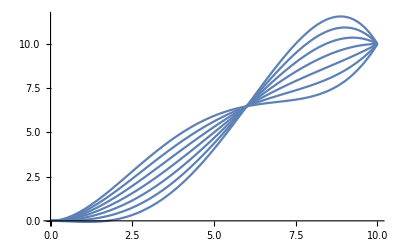

```mathematica
Plot[Table[v[t]/.sol/.{T-> 10, v0->0,a0->0,sf->50,vf->10,af->k},{k,-3,3,1}],{t,0,10}]
```

### Stopping Primitive analysis

#### Stopping primitives with cost function

In order to prevent the solution from rolling up

```mathematica
Manipulate[Manipulate[Grid@{{
If[a0>0 || a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001, Show[
Plot[sEval[t,v0,a0,sf,0,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]],{t,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]},PlotRange->All,PlotLabel->"Position Profile",AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium]
]],
If[a0>0 || a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001, Show[
Plot[vEval[t,v0,a0,sf,0,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]],{t,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]},PlotRange->All,PlotLabel->"Velocity Profile",AxesLabel->{"t (s)","v[t] (m/s)"},ImageSize->Medium]
]],
If[a0>0 || (a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001), Show[
ParametricPlot[{sEval[t,v0,a0,sf,0,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]],vEval[t,v0,a0,sf,0,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]]},{t,0,Max[0.1,finalOptTimeStop[v0,a0,sf]+dt]},PlotRange->All,PlotLabel->"Velocity Profile",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio]
]],(*finalOptTimeStop[v0,a0,sf]//N,evalPrimitiveCoeffs[v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]]//N*)
}},{{sf,20},1,100}],{{v0,10},1,10},{{a0,-3},-3,3},{{dt,0},-1,1}]
```

We find the optimal time to stop

```mathematica
Manipulate[Manipulate[Grid@{{
Show[
Plot[totalCost[v0,a0,sf,0,0,t],{t,0,80},PlotRange->If[a0>0 || a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001,{0,totalCost[v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]]+2},Automatic],ImageSize->Medium,PlotLabel->"Cost ∫J(T\!\(\*SuperscriptBox[\()\), \(2\)]\)",AxesLabel->{"T (s)","∫\!\(\*SuperscriptBox[\(J\), \(2\)]\)"}],
If[a0>0 || a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001, 
Graphics[{Red,Thick,Line[{{finalOptTimeStop[v0,a0,sf]+dt,0},{finalOptTimeStop[v0,a0,sf]+dt,10000}}],Text[Style["Optimal Time to Stop",Medium],{finalOptTimeStop[v0,a0,sf]+1+dt,totalCost[v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]+dt]+4},Left]}],
{}]],
If[a0>0 || a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001, Show[
Plot[sEval[t,v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]+dt],{t,0,finalOptTimeStop[v0,a0,sf]+dt},PlotRange->All,PlotLabel->"Position Profile",AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium]
]],
If[a0>0 || (a0 < 0 && sf<= (4 v0^2)/(-5 a0)-0.001), Show[
ParametricPlot[{sEval[t,v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]+dt],vEval[t,v0,a0,sf,0,0,finalOptTimeStop[v0,a0,sf]+dt]},{t,0,finalOptTimeStop[v0,a0,sf]+dt},PlotRange->All,PlotLabel->"Velocity Profile",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio]
]]

}},{{sf,0.1},-10,100}],{{v0,5},1,10},{{a0,-2},-3,3},{{dt,0},-5,5}]
```

#### Stopping Primitive with j0 = 0

```mathematica
Manipulate[Block[{coefTStop,sfStop,TStop, coefJ0Stop,sfJ0Stop,TJ0Stop = 0.},
{coefTStop,sfStop,TStop}=StopPrimitive[vv0, aa0, ssf];
If[vv0 > 0 && aa0 < 0 && coefTStop[[4]] > 0,
	{coefJ0Stop,sfJ0Stop,TJ0Stop} = StopPrimitiveJ00[vv0, aa0];
];
Grid@{{
Quiet@Show[
If[TStop != 0, Plot[Legended[sEval[t,vv0,aa0,sfStop,0,0,TStop],Placed["Stop(\!\(\*SubscriptBox[\(a\), \(0\)]\),\!\(\*SubscriptBox[\(v\), \(0\)]\),\!\(\*SubscriptBox[\(s\), \(f\)]\))",Below]],{t,0,TStop},PlotRange->All,PlotLabel->"Position Profile",AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium],{}],
If[TJ0Stop != 0,
Plot[sEval[t,vv0,aa0,sfJ0Stop,0,0,TJ0Stop],{t,0,TJ0Stop},PlotStyle->{ColorData[97,"ColorList"][[2]]}],{}
]],
Quiet@Show[
If[TStop != 0, ParametricPlot[{sEval[t,vv0,aa0,sfStop,0,0,TStop],vEval[t,vv0,aa0,sfStop,0,0,TStop]},{t,0,TStop},PlotRange->All,PlotLabel->"Velocity Profile",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio],{}],
If[TJ0Stop != 0,
ParametricPlot[{sEval[t,vv0,aa0,sfJ0Stop,0,0,TJ0Stop],vEval[t,vv0,aa0,sfJ0Stop,0,0,TJ0Stop]},{t,0,TJ0Stop},PlotStyle->{ColorData[97,"ColorList"][[2]]}]
,{}
]
]
},{
Quiet@Show[
If[vv0!=0,Plot[1,{x,coefTStop[[4]]-2.5,coefTStop[[4]]},AspectRatio->0.2,ImageSize->Large,PlotStyle->{ColorData[97,"ColorList"][[4]]}],{}],
If[vv0!=0,Graphics[{ColorData[97,"ColorList"][[4]],PointSize[Medium],Point[{coefTStop[[4]],1}]}],{}],
If[TJ0Stop != 0,Graphics[{ColorData[97,"ColorList"][[5]],PointSize[Medium],Point[{coefJ0Stop[[4]],1}]}],{}]
],SpanFromLeft
}}],{{vv0,5},0,10},{{aa0,-2},-3,3},{{ssf,25},0.1,200}]
```

### Pass Primitive analysis

#### Optimal time solution

Is the optimal time for reaching the final velocity, there is two possibility but the smaller solution is the one we want to use

```mathematica
Manipulate[Grid[{{
Show[
Plot[{vvf,finalOptVel[v0,aa0,sf,T]/.{v0->10,sf->20}},{T,0,100},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotStyle->{Green,Blue},AxesLabel->{"time to reach vf (s)","final velocity (m/\!\(\*SuperscriptBox[\(s\), \(2\)]\))"}],
ListLinePlot[{{T/.eqFinalOptTimeT[[1]]/.{v0->10,sf->20,a0->aa0,vf->vvf},-5},{T/.eqFinalOptTimeT[[1]]/.{v0->10,sf->20,a0->aa0,vf->vvf},vvf+10}},ImageSize->Medium,PlotStyle->{Red,Thick}],
ListLinePlot[{{T/.eqFinalOptTimeT[[2]]/.{v0->10,sf->20,a0->aa0,vf->vvf},-5},{T/.eqFinalOptTimeT[[2]]/.{v0->10,sf->20,a0->aa0,vf->vvf},vvf+10}},ImageSize->Medium,PlotStyle->{Green,Thick}],
Graphics[{Text["\!\(\*SubscriptBox[\(v\), \(f\)]\)",{100,vvf},Bottom]}]
],eqFinalOptTimeT/.{v0->10,sf->20,a0->aa0,vf->vvf}//N
}}],{{aa0,-1,"\!\(\*SubscriptBox[\(a\), \(0\)]\)"},-5,2},{{vvf,0,"\!\(\*SubscriptBox[\(v\), \(f\)]\)"},0,15}]
```

These define two limit of velocityies

```mathematica
finalOptVel[v0,a0,sf,T2]/.{v0->10,a0->-2,sf->50,T2->5}//N
```

11.25

```mathematica
finalOptVel[v0,a0,sf,T2]/.{v0->10,a0->-2,sf->50,T2->3}//N
```

23.25

#### Optimal solution analysis of the second solution

Why we use the first solution of the equation

```mathematica
Manipulate[Block[{T1,T2},
T1 = T/.eqFinalOptTimeT[[1]]/.{v0->vv0,sf->ssf,a0->aa0,vf->vvf};
T2 = T/.eqFinalOptTimeT[[2]]/.{v0->vv0,sf->ssf,a0->aa0,vf->vvf};
Grid[{{
Show[
Plot[{vvf,finalOptVel[vv0,aa0,ssf,T]},{T,0,100},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotStyle->{Green,Blue},AxesLabel->{"time to reach vf (s)","final velocity (m/\!\(\*SuperscriptBox[\(s\), \(2\)]\))"}],
ListLinePlot[{{T1,-5},{T1,vvf+10}},ImageSize->Medium,PlotStyle->{Red,Thick}],
ListLinePlot[{{T2,-5},{T2,vvf+10}},ImageSize->Medium,PlotStyle->{Green,Thick}],
Graphics[{Text["\!\(\*SubscriptBox[\(v\), \(f\)]\)",{100,vvf},Bottom]}]
],{T1,T2}//N,
Show[
ParametricPlot[Evaluate@{sEval[t,vv0,aa0,ssf,vvf,0,T1],vEval[t,vv0,aa0,ssf,vvf,0,T1]},{t,0,T1},
PlotLabel->"Velocity",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotRange->{{-10,ssf},{-10,20}},PlotStyle->{ColorData[97,"ColorList"][[1]]}],
ParametricPlot[Evaluate@{sEval[t,vv0,aa0,ssf,vvf,0,T2],vEval[t,vv0,aa0,ssf,vvf,0,T2]},{t,0,T2},
PlotLabel->"Velocity",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotRange->{{-10,ssf},{-10,20}},PlotStyle->{ColorData[97,"ColorList"][[2]]}]
]
}}]
],{{vv0,4,"\!\(\*SubscriptBox[\(v\), \(0\)]\)"},0,30},{{aa0,-1,"\!\(\*SubscriptBox[\(a\), \(0\)]\)"},-5,5},{{ssf,10,"\!\(\*SubscriptBox[\(s\), \(f\)]\)"},0,100},{{vvf,20,"\!\(\*SubscriptBox[\(v\), \(f\)]\)"},0,30}]
```

#### Find the [T1,T2] time interval if a0>0 (final velocity - final time)

We don' t have the vstar

```mathematica
Manipulate[
Grid[{{
Show[
Plot[{vvfmin,vvfmax,finalOptVel[vv0,aa0,xxf,T]},{T,0,Tmax+10},AxesLabel->{"Final Time","Final velocity"}, ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotStyle->{Green,Green,Blue},Filling->{1->{2}},PlotRange->{All,{vvfmin-3,vvfmax+3}}],
RegionPlot[Max[Tmin,finalOptTime[vv0,aa0,xxf,vvfmax]]<x<Min[Tmax,finalOptTime[vv0,aa0,xxf,vvfmin]],{x,Tmin,Tmax},{y,vvfmin-3,vvfmax+3}],
Graphics[{Green,Thick,Line[{{finalOptTime[vv0,aa0,xxf,vvfmin],vvfmin-3},{finalOptTime[vv0,aa0,xxf,vvfmin],vvfmax+3}}]}],
Graphics[{Green,Thick,Line[{{finalOptTime[vv0,aa0,xxf,vvfmax],vvfmin-3},{finalOptTime[vv0,aa0,xxf,vvfmax],vvfmax+3}}]}],
Graphics[{Red,Thick,Line[{{Tmin,vvfmin-3},{Tmin,vvfmax+3}}]}],
Graphics[{Red,Thick,Line[{{Tmax,vvfmin-3},{Tmax,vvfmax+3}}]}],
Graphics[Text[Style["Tmin",Red,Medium],{Tmin-0.5,vvfmax+2.5},Right]],
Graphics[Text[Style["Tmax",Red,Medium],{Tmax+0.5,vvfmax+2.5},Left]],
Graphics[Text[Style["T1",Green,Bold,Medium],{finalOptTime[vv0,aa0,xxf,vvfmax]-0.5,vvfmin-2.5},Right]],
Graphics[Text[Style["T2",Green,Bold,Medium],{finalOptTime[vv0,aa0,xxf,vvfmin]+0.5,vvfmin-2.5},Left]],
If[Max[Tmin,finalOptTime[vv0,aa0,xxf,vvfmax]]<Min[Tmax,finalOptTime[vv0,aa0,xxf,vvfmin]],
Graphics[Text[Style["[\!\(\*SubscriptBox[\(T\), \(1\)]\),\!\(\*SubscriptBox[\(T\), \(2\)]\)]",Red,Medium],{(Max[Tmin,finalOptTime[vv0,aa0,xxf,vvfmax]]+Min[Tmax,finalOptTime[vv0,aa0,xxf,vvfmin]])/2,vvfmin-0.7},Center]],{}
]
]
}}],{{vv0,10,"v0"},5,20},{{aa0,0,"a0"},-5,5},{{xxf,40,"sf"},10,50},{{vvfmin,5,"\!\(\*SubscriptBox[\(vf\), \(min\)]\)"},0,vvfmax},{{vvfmax,15,"\!\(\*SubscriptBox[\(vf\), \(max\)]\)"},vvfmin,25},{{Tmin,4,"Tmin"},1,Tmax},{{Tmax,10,"Tmax"},Tmin,50}]
```

#### Test Pass Primitive: Find the [T1,T2] interval (final velocity - final time)

```mathematica
Manipulate[Block[{yMin=-2, yMax=25, T1, T2, v1, v2, Tvmin, Tvmax, coefT1, coefT2},
{coefT2,v2,{Tvmin,T2},coefT1,v1,{Tvmax,T1}}=PassPrimitive[vv0,  aa0, xxf, vvfmin, vvfmax, Tmin, Tmax];
Grid[{{
Show[
Plot[{vvfmin,vvfmax,finalOptVel[vv0,aa0,xxf,T]},{T,0,Tmax+10},ImageSize->Large,AspectRatio->1/GoldenRatio,PlotStyle->{Green,Green,Blue},PlotRange->{{0,Tmax+10},{yMin,yMax}},AxesLabel->{"time to reach vf (s)","final velocity (m/\!\(\*SuperscriptBox[\(s\), \(2\)]\))"}],
Graphics[Text[Style["\!\(\*SubscriptBox[\(v\), \(min\)]\)",Green,Bold,Medium],{0.1,vvfmin-1},Left]],
Graphics[Text[Style["\!\(\*SubscriptBox[\(v\), \(max\)]\)",Green,Bold,Medium],{0.1,vvfmax+1},Left]],
RegionPlot[T1<x<T2,{x,Tmin,Tmax},{y,yMin,yMax}],
RegionPlot[v2<y<v1,{x,0,Tmax+10},{y,yMin,yMax},PlotStyle->{Opacity[0.5],LightGreen}],
Graphics[{Green,Thick,Line[{{Tvmax,yMin},{Tvmax,yMax}}]}],
Graphics[Text[Style["Tvmax",Green,Bold,Medium],{Tvmax-0.5,yMin+1},Right]],
Graphics[{Green,Thick,Line[{{Tvmin,yMin},{Tvmin,yMax}}]}],
Graphics[Text[Style["Tvmin",Green,Bold,Medium],{Tvmin+0.5,yMin+1},Left]],
Graphics[{Red,Thick,Line[{{Tmin,yMin},{Tmin,yMax}}]}],
Graphics[{Red,Thick,Line[{{Tmax,yMin},{Tmax,yMax}}]}],
Graphics[Text[Style["Tmin",Red,Medium],{Tmin-0.5,yMax-1},Right]],
Graphics[Text[Style["Tmax",Red,Medium],{Tmax+0.5,yMax-1},Left]],
If[aa0<0,
{Graphics[{Brown,Thick,Line[{{0,finalOptVel[vv0,aa0,xxf,finalOptTimeMin[aa0,xxf]]},{Tmax+10,finalOptVel[vv0,aa0,xxf,finalOptTimeMin[aa0,xxf]]}}]}],
Graphics[{Brown,Thick,Line[{{finalOptTimeMin[aa0,xxf],yMin},{finalOptTimeMin[aa0,xxf],yMax}}]}],
Graphics[Text[Style["\!\(\*SuperscriptBox[\(v\), \(*\)]\)",Brown,Bold,Medium],{finalOptTimeMin[aa0,xxf]-0.2,yMax-3},Right]]}
,
{}
],
If[T1!=0 && T1<=T2,
Graphics[Text[Style["[\!\(\*SubscriptBox[\(T\), \(1\)]\),\!\(\*SubscriptBox[\(T\), \(2\)]\)]",Red,Medium],{(T1+T2)/2,vvfmin-0.7},Center]],{}
]
],PassPrimitive[vv0,  aa0, xxf, vvfmin, vvfmax, Tmin, Tmax]//N
}}]],{{vv0,14.25,"v0"},2,20},{{aa0,0,"a0"},-8,5},{{xxf,6.7,"sf"},0.5,50},{{vvfmin,5,"\!\(\*SubscriptBox[\(vf\), \(min\)]\)"},0,vvfmax},{{vvfmax,14.25,"\!\(\*SubscriptBox[\(vf\), \(max\)]\)"},vvfmin,25},{{Tmin,0.5,"Tmin"},0.1,Tmax-0.01},{{Tmax,10.1,"Tmax"},Tmin+0.01,50}]
```

#### Test Pass Primitive : [T1, T2] interval, primitives, and feasible jerk

```mathematica
Manipulate[Block[{yMin=-2, yMax=25, T1, T2, v1, v2, Tvmin, Tvmax, coefT1, coefT2},
{coefT2,v2,{Tvmin,T2},coefT1,v1,{Tvmax,T1}}=PassPrimitive[vv0,  aa0, ssf, vvfmin, vvfmax, Tmin, Tmax];
Grid[{{
Show[
Plot[{vvfmin,vvfmax,finalOptVel[vv0,aa0,ssf,T]},{T,0,Tmax+10},ImageSize->Large,AspectRatio->1/GoldenRatio,PlotStyle->{Green,Green,Blue},PlotRange->{{0,Tmax+10},{yMin,yMax}},AxesLabel->{"time to reach vf (s)","final velocity (m/\!\(\*SuperscriptBox[\(s\), \(2\)]\))"}],
Graphics[Text[Style["\!\(\*SubscriptBox[\(v\), \(min\)]\)",Green,Bold,Medium],{0.1,vvfmin-1},Left]],
Graphics[Text[Style["\!\(\*SubscriptBox[\(v\), \(max\)]\)",Green,Bold,Medium],{0.1,vvfmax+1},Left]],
RegionPlot[T1<x<T2,{x,Tmin,Tmax},{y,yMin,yMax}],
RegionPlot[v2<y<v1,{x,0,Tmax+10},{y,yMin,yMax},PlotStyle->{Opacity[0.5],LightGreen}],
Graphics[{Green,Thick,Line[{{Tvmax,yMin},{Tvmax,yMax}}]}],
Graphics[Text[Style["Tvmax",Green,Bold,Medium],{Tvmax-0.5,yMin+1},Right]],
Graphics[{Green,Thick,Line[{{Tvmin,yMin},{Tvmin,yMax}}]}],
Graphics[Text[Style["Tvmin",Green,Bold,Medium],{Tvmin+0.5,yMin+1},Left]],
Graphics[{Red,Thick,Line[{{Tmin,yMin},{Tmin,yMax}}]}],
Graphics[{Red,Thick,Line[{{Tmax,yMin},{Tmax,yMax}}]}],
Graphics[Text[Style["Tmin",Red,Medium],{Tmin-0.5,yMax-1},Right]],
Graphics[Text[Style["Tmax",Red,Medium],{Tmax+0.5,yMax-1},Left]],
If[aa0<0,
{Graphics[{Brown,Thick,Line[{{0,finalOptVel[vv0,aa0,ssf,finalOptTimeMin[aa0,ssf]]},{Tmax+10,finalOptVel[vv0,aa0,ssf,finalOptTimeMin[aa0,ssf]]}}]}],
Graphics[{Brown,Thick,Line[{{finalOptTimeMin[aa0,ssf],yMin},{finalOptTimeMin[aa0,ssf],yMax}}]}],
Graphics[Text[Style["\!\(\*SuperscriptBox[\(v\), \(*\)]\)",Brown,Bold,Medium],{finalOptTimeMin[aa0,ssf]-0.2,yMax-3},Right]]}
,
{}
],
If[T1!=0 && T1<=T2,
Graphics[Text[Style["[\!\(\*SubscriptBox[\(T\), \(1\)]\),\!\(\*SubscriptBox[\(T\), \(2\)]\)]",Red,Medium],{(T1+T2)/2,vvfmin-0.7},Center]],{}
]
],
If[T1!= 0 && T1<=T2,
Grid[{{
Show[
Plot[sEval[t,vv0,aa0,ssf,v2,0,T2],{t,0,T2},PlotRange->All,PlotLabel->"Position Primitive",AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium,AspectRatio->1/GoldenRatio],
Plot[sEval[t,vv0,aa0,ssf,v1,0,T1],{t,0,T1},PlotRange->All,AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotStyle->{ColorData[97,"ColorList"][[2]],Thick}]
,PlotRange->All],
Show[
ParametricPlot[{Evaluate@{sEval[t,vv0,aa0,ssf,v1,0,T1],vEval[t,vv0,aa0,ssf,v1,0,T1]},
Evaluate@{sEval[t,vv0,aa0,ssf,v2,0,T2],vEval[t,vv0,aa0,ssf,v2,0,T2]}},{t,0,Max[T1,T2]},PlotLabel->"Velocity Primitive",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotRange->{{0,ssf},{0,10+Max[vv0,v1,v2]}}]
]
},{
Show[
Plot[1,{x,Min[coefT2[[4]],coefT1[[4]]],Max[coefT2[[4]],coefT1[[4]]]},AspectRatio->0.2,ImageSize->Large,
PlotRange->{{Min[-5,coefT2[[4]],coefT1[[4]]]-5,Max[5,coefT2[[4]],coefT1[[4]]]+5},{0,2}},AxesLabel->{"\!\(\*SubscriptBox[\(j\), \(0\)]\) (m/\!\(\*SuperscriptBox[\(s\), \(3\)]\))",""},PlotLabel->"Feasible \!\(\*SubscriptBox[\(j\), \(0\)]\)"],
Graphics[{ColorData[97,"ColorList"][[1]],PointSize[Medium],Point[{Min[coefT2[[4]],coefT1[[4]]],1}]}],
Graphics[{ColorData[97,"ColorList"][[1]],PointSize[Medium],Point[{Max[coefT2[[4]],coefT1[[4]]],1}]}]
],SpanFromLeft
}}]
],{coefT2,v2,{Tvmin,T2},coefT1,v1,{Tvmax,T1}}
}}]],{{vv0,0,"v0"},0,20},{{aa0,0,"a0"},-8,5},{{ssf,70,"sf"},10,100},{{vvfmin,14.5,"\!\(\*SubscriptBox[\(vf\), \(min\)]\)"},0,vvfmax},{{vvfmax,15.5,"\!\(\*SubscriptBox[\(vf\), \(max\)]\)"},vvfmin,25},{{Tmin,1,"Tmin"},1,Tmax-0.01},{{Tmax,50,"Tmax"},Tmin+0.01,50}]
```

#### Pass Primitive with j0 = 0

```mathematica
Manipulate[Block[{yMin=-2, yMax=25, T1, T2, TJ0, v1, v2, vJ0, Tvmin, Tvmax, coefT1, coefT2, coefJ0},
{coefT2,v2,{Tvmin,T2},coefT1,v1,{Tvmax,T1}}=PassPrimitive[vv0,  aa0, ssf, vvfmin, vvfmax, Tmin, Tmax];
If[coefT2[[4]]< 0 <coefT1[[4]] || coefT1[[4]]< 0 <coefT2[[4]],
	{coefJ0,vJ0,TJ0}= PassPrimitiveJ00[vv0, aa0, ssf, vvfmin, vvfmax];
];
Grid[{{
If[T1!=0 && T1<=T2,Show[
Plot[jEval[0,vv0,aa0,ssf,vf,0,Quiet@finalOptTime[vv0,aa0,ssf,vf]],{vf,v2,v1},ImageSize->Medium,PlotLabel->"J0[\!\(\*SubscriptBox[\(v\), \(f\)]\)]",AxesLabel->{"vf","j0"}],
Graphics[{ColorData[97,"ColorList"][[1]],PointSize[Medium],Line[{{v2,jEval[0,vv0,aa0,ssf,v1,0,Quiet@finalOptTime[vv0,aa0,ssf,v1]]},{v1,jEval[0,vv0,aa0,ssf,v1,0,Quiet@finalOptTime[vv0,aa0,ssf,v1]]}}]}],
Graphics[{ColorData[97,"ColorList"][[2]],PointSize[Medium],Line[{{v2,jEval[0,vv0,aa0,ssf,v2,0,Quiet@finalOptTime[vv0,aa0,ssf,v2]]},{v1,jEval[0,vv0,aa0,ssf,v2,0,Quiet@finalOptTime[vv0,aa0,ssf,v2]]}}]}]
]],
If[T1!=  0 && T1<=T2,
Grid[{{
Show[
Plot[sEval[t,vv0,aa0,ssf,v1,0,T1],{t,0,T1},PlotRange->All,PlotLabel->"Position Primitive",AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium,AspectRatio->1/GoldenRatio],
Plot[sEval[t,vv0,aa0,ssf,v2,0,T2],{t,0,T2},PlotRange->All,AxesLabel->{"t (s)","x[t] (m)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotStyle->{ColorData[97,"ColorList"][[2]],Thick}],
If[coefT2[[4]]< 0 <coefT1[[4]] || coefT1[[4]]< 0 <coefT2[[4]], 
Plot[sEval[t,vv0,aa0,ssf,vJ0,0,TJ0],{t,0,TJ0},PlotStyle->{ColorData[97,"ColorList"][[3]],Thick}],
{}]
, PlotRange->All
],
Show[
ParametricPlot[Evaluate@{sEval[t,vv0,aa0,ssf,v1,0,T1],vEval[t,vv0,aa0,ssf,v1,0,T1]},
{t,0,T1},PlotLabel->"Velocity Primitive",AxesLabel->{"x (m)","v[x] (m/s)"},ImageSize->Medium,AspectRatio->1/GoldenRatio,PlotRange->{{0,ssf},{0,10+Max[vv0,v1,v2]}}],
ParametricPlot[Evaluate@{sEval[t,vv0,aa0,ssf,v2,0,T2],vEval[t,vv0,aa0,ssf,v2,0,T2]},{t,0,T2},PlotStyle->{ColorData[97,"ColorList"][[2]]}],
If[coefT2[[4]]< 0 <coefT1[[4]] || coefT1[[4]]< 0 <coefT2[[4]],
ParametricPlot[
Evaluate@{sEval[t,vv0,aa0,ssf,vJ0,0,TJ0],vEval[t,vv0,aa0,ssf,vJ0,0,TJ0]},{t,0,TJ0},PlotStyle->{ColorData[97,"ColorList"][[3]],Thick}]
,{}]]
},{
Show[
If[coefT2[[4]] != coefT1[[4]], Plot[1,{x,Min[coefT2[[4]],coefT1[[4]]],Max[coefT2[[4]],coefT1[[4]]]},AspectRatio->0.2,ImageSize->Large,
PlotRange->{{Min[coefT2[[4]],coefT1[[4]]]-0.1,Max[coefT2[[4]],coefT1[[4]]]+0.1},{0,2}},AxesLabel->{"\!\(\*SubscriptBox[\(j\), \(0\)]\) (m/\!\(\*SuperscriptBox[\(s\), \(3\)]\))",""},PlotLabel->"Feasible \!\(\*SubscriptBox[\(j\), \(0\)]\)",PlotStyle->{ColorData[97,"ColorList"][[3]]}],{}],
Graphics[{
If[Min[coefT2[[4]],coefT1[[4]]] == coefT1[[4]],
	ColorData[97,"ColorList"][[1]]
,
	ColorData[97,"ColorList"][[2]]
]
,PointSize[Medium],Point[{Min[coefT2[[4]],coefT1[[4]]],1}]}],
Graphics[{
If[Max[coefT2[[4]],coefT1[[4]]] == coefT1[[4]],
	ColorData[97,"ColorList"][[1]]
,
	ColorData[97,"ColorList"][[2]]
]
,PointSize[Medium],Point[{Max[coefT2[[4]],coefT1[[4]]],1}]}]
],SpanFromLeft
}}]
]
}}]],{{vv0,0.,"v0"},0,20},{{aa0,0.,"a0"},-8,5},{{ssf,43,"sf"},10,50},{{vvfmin,1,"\!\(\*SubscriptBox[\(vf\), \(min\)]\)"},0,vvfmax},{{vvfmax,15,"\!\(\*SubscriptBox[\(vf\), \(max\)]\)"},vvfmin,25},{{Tmin,4,"Tmin"},0,Tmax-0.01},{{Tmax,10,"Tmax"},Tmin+0.01,50}]
```

```mathematica
Manipulate[Block[{yMin = -2, yMax = 25, T1, T2, TJ0, v1, v2, vJ0, Tvmin, Tvmax, coefT1, coefT2, coefJ0},{coefT2, v2, {Tvmin, T2}, coefT1, v1, {Tvmax, T1}} = PassPrimitive[vv0, aa0, ssf, vvfmin, vvfmax, Tmin, Tmax]; 
If[coefT2[[4]] < 0 < coefT1[[4]] || coefT1[[4]] < 0 < coefT2[[4]], 
{coefJ0, vJ0, TJ0} = PassPrimitiveJ00[vv0, aa0, ssf, vvfmin, vvfmax]; 
]; 
Grid[{{If[T1 != 0 && T1 <= T2,Show[Plot[jEval[0, vv0, aa0, ssf, vf, 0,Quiet[finalOptTime[vv0, aa0, ssf, vf]]], {vf, v2, v1}, ImageSize -> Medium, PlotLabel -> "J0[\!\(\*SubscriptBox[\(v\), \(f\)]\)]",AxesLabel -> {"vf", "j0"}], Graphics[{ColorData[97, "ColorList"][[1]], PointSize[Medium], Line[{{v2, jEval[0, vv0, aa0, ssf, v1, 0,Quiet[finalOptTime[vv0, aa0, ssf, v1]]]},{v1, jEval[0, vv0, aa0, ssf, v1, 0,Quiet[finalOptTime[vv0, aa0, ssf, v1]]]}}]}], 
Graphics[{ColorData[97, "ColorList"][[2]], PointSize[Medium], Line[{{v2, jEval[0, vv0, aa0, ssf, v2, 0, Quiet[finalOptTime[vv0, aa0, ssf, v2]]]}, {v1, jEval[0, vv0, aa0, ssf, v2, 0,Quiet[finalOptTime[vv0, aa0, ssf, v2]]]}}]}]]
], If[T1 != 0 && T1 <= T2, Grid[{{Show[Plot[sEval[t, vv0, aa0, ssf, v1, 0, T1], {t, 0, T1}, PlotRange -> All, PlotLabel -> "Position Primitive", AxesLabel -> {"t (s)", "x[t] (m)"}, ImageSize -> Medium, AspectRatio -> 1/GoldenRatio], Plot[sEval[t, vv0, aa0, ssf, v2, 0,T2], {t, 0, T2}, PlotRange -> All, AxesLabel ->{"t (s)", "x[t] (m)"}, ImageSize -> Medium, AspectRatio -> 1/GoldenRatio, PlotStyle -> {ColorData[97, "ColorList"][[2]], Thick}],If[coefT2[[4]] < 0 < coefT1[[4]] || coefT1[[4]] < 0 < coefT2[[4]], 
Plot[sEval[t, vv0, aa0, ssf, vJ0, 0,TJ0], {t, 0, TJ0}, PlotStyle -> {ColorData[97, "ColorList"][[3]], Thick}], {}], PlotRange -> All],Show[ParametricPlot[Evaluate[{sEval[t, vv0, aa0, ssf, v1, 0, T1],vEval[t, vv0, aa0, ssf, v1, 0, T1]}], {t, 0, T1},           PlotLabel -> "Velocity Primitive", AxesLabel -> {"x (m)", "v[x] (m/s)"}, ImageSize -> Medium, AspectRatio -> 1/GoldenRatio, PlotRange -> {{0, ssf}, {0, 10 + Max[vv0, v1, v2]}}],ParametricPlot[Evaluate[{sEval[t, vv0, aa0, ssf, v2, 0, T2], vEval[t, vv0, aa0, ssf, v2, 0, T2]}], {t, 0, T2}, PlotStyle -> {ColorData[97, "ColorList"][[2]]}], 
If[coefT2[[4]] < 0 < coefT1[[4]] || coefT1[[4]] < 0 < coefT2[[4]], 
ParametricPlot[Evaluate[{sEval[t, vv0, aa0, ssf, vJ0, 0, TJ0], vEval[t,vv0, aa0, ssf, vJ0, 0, TJ0]}], {t, 0, TJ0}, PlotStyle -> {ColorData[97, "ColorList"][[3]], Thick}], {}]]
},{Show[If[coefT2[[4]] != coefT1[[4]], Plot[1, {x, Min[coefT2[[4]], coefT1[[4]]], Max[coefT2[[4]], coefT1[[4]]]}, AspectRatio -> 0.2, ImageSize -> Large, PlotRange -> {{Min[coefT2[[4]], coefT1[[4]]] - 0.1, Max[coefT2[[4]], coefT1[[4]]] + 0.1}, {0, 2}},AxesLabel -> {"\!\(\*SubscriptBox[\(j\), \(0\)]\) \(m/\!\(\*SuperscriptBox[\(s\), \(3\)]\))", ""}, PlotLabel -> "Feasible \!\(\*SubscriptBox[\(j\), \(0\)]\)", PlotStyle -> {ColorData[97, "ColorList"][[3]]}], {}], Graphics[{If[Min[coefT2[[4]], coefT1[[4]]] == coefT1[[4]], ColorData[97, "ColorList"][[1]], ColorData[97, "ColorList"][[2]]], PointSize[Medium], Point[{Min[coefT2[[4]], coefT1[[4]]], 1}]}], Graphics[{If[Max[coefT2[[4]], coefT1[[4]]] == coefT1[[4]], ColorData[97, "ColorList"][[1]], ColorData[97, "ColorList"][[2]]], PointSize[Medium], Point[{Max[coefT2[[4]], coefT1[[4]]], 1}]}]], SpanFromLeft}
}]]}}]], {{vv0, 0., "v0"}, 0, 20}, {{aa0, 2.4399999999999995, "a0"}, -8, 5}, {{ssf, 46.45, "sf"}, 10, 50}, {{vvfmin, 1, "\!\(\*SubscriptBox[\(vf\), \(min\)]\)"}, 0, Dynamic[vvfmax]},{{vvfmax, 15, "\!\(\*SubscriptBox[\(vf\), \(max\)]\)"}, 
  Dynamic[vvfmin], 25}, {{Tmin, 4, "Tmin"}, 0, Dynamic[Tmax - 0.01]}, {{Tmax, 10, "Tmax"}, Dynamic[Tmin + 0.01], 50}]
```